```mathematica
A=(J(J+1)-L(L+1)-S(S+1))*(2J+1)
```

(1+2 J) (J (1+J)-L (1+L)-S (1+S))

```mathematica
Sum[(2J+1)*(J(J+1)-L(L+1)-S(S+1)),{J,L-S,L+S}]
```

0

```mathematica
Sum[(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-S(S+1)),{J',-S,S}]
```

0

```mathematica
Sum[(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-S(S+1)),{J',a,b}]//FullSimplify
```

-1/2 (-1+a-b) (1+a+b+2 L) (a^2+b (2+b)+2 (a+b) L-2 S (1+S))

```mathematica
Sum[(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-1/2(1/2+1)),{J',-1/2,1/2}]//FullSimplify
```

0

```mathematica
Sum[(2*(J'+L)+1),{J',a,b}]
```

-((-1+a-b) (1+a+b+2 L))

```mathematica
bottom=(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-n/2(n/2+1))/.{J'->-(n+1)/2}//FullSimplify
```

-1/4 (2 L-n) (1+2 n+4 L (1+n))

```mathematica
top=(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-n/2(n/2+1))/.{J'->+(n+1)/2}//FullSimplify
```

1/4 (2+2 L+n) (3+2 n+4 L (1+n))

```mathematica
top+bottom//FullSimplify
```

1/2 (1+2 L) (3+2 n (2+n))

```mathematica
mid=-Sum[(2*(J'+L)+1)*(-1/2)*(n+3/2),{J',-(n+1)/2,(n+1)/2}]//FullSimplify
```

1/4 (1+2 L) (2+n) (3+2 n)

```mathematica
(1/2)(top+bottom)+mid//FullSimplify
```

1/4 (1+2 L) (9+n (11+4 n))

```mathematica
Sum[(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-(n/2)((n/2)+1)-2*(n/2+1)),{J',-n/2-1,n/2+1}]//FullSimplify
```

0

```mathematica
mid=Sum[(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-(n/2)((n/2)+1)),{J',-n/2,n/2}]+Sum[(2(J'+L)+1)*-2*(n/2+1),{J',-n/2-1,n/2+1}]//FullSimplify
```

-((1+2 L) (2+n) (3+n))

```mathematica
top=(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-(n/2)((n/2)+1))/.{J'->n/2+1}//FullSimplify
```

(1+L) (2+n) (3+2 L+n)

```mathematica
bottom=(2(J'+L)+1)*((J'+L)((J'+L)+1)-L(L+1)-(n/2)((n/2)+1))/.{J'->-n/2-1}//FullSimplify
```

-L (-1+2 L-n) (2+n)

```mathematica
top+bottom//FullSimplify
```

(1+2 L) (2+n) (3+n)

```mathematica
top+bottom+mid//FullSimplify
```

0

```mathematica
Lx*Sx+Ly*Sy/.{Lx->(1/2)*(Lp+Lm),Ly->(1/(2*I))*(Lp-Lm),Sx->(1/2)*(Sp+Sm),Sy->(1/(2*I))*(Sp-Sm)}//FullSimplify
```

1/2 (Lp Sm+Lm Sp)

```mathematica
Sum[Sum[mL*mS,{mL,-L,L}],{mS,-S,S}]
```

0

```mathematica
(1/2)*(S*(S+1)-3/4-3/4)/.{S->-1}
```

-3/4

```mathematica
(1/2)*(S*(S+1)-3/4-3/4)/.{S->0}
```

-3/4

```mathematica
(1/2)*(S*(S+1)-3/4-3/4)/.{S->1}
```

1/4

```mathematica
-1/2*3/2+3/2*(2-3/2)
```

0

```mathematica
-(1+1)-(1/2)*(1/2+1)
```

-11/4

```mathematica
(1/2)*(j2(j2+1)-(1+1)-(1/2)*(1/2+1))/.{j2->1/2}
```

-1

```mathematica
(1/2)*(j2(j2+1)-(1+1)-(1/2)*(1/2+1))/.{j2->3/2}
```

1/2

```mathematica
(2*j2+1)/2*(j2*(j2+1)-11/4)/.{j2->1/2}
```

-2

```mathematica
(2*j2+1)/2*(j2*(j2+1)-11/4)/.{j2->3/2}
```

2

```mathematica
(2/2+1)/2*(1/2*(1/2+1)-11/4)+4/2*(3/2*(3/2+1)-11/4)
```

0

```mathematica
(2*J+1)/2*(J*(J+1)-1(1+1))/.{J->1}
```

0

```mathematica
(*Part c*)
```

```mathematica
1/2*(J*(J+1)-1(1+1)-1(1+1))/.{J->0}
```

-2

```mathematica
1/2*(J*(J+1)-1(1+1)-1(1+1))/.{J->1}
```

-1

```mathematica
1/2*(J*(J+1)-1(1+1)-1(1+1))/.{J->2}
```

1

```mathematica
(*Part d*)
```

```mathematica
(s2*(s2+1)+(1/2)*(j2*(j2+1)-l2*(l2+1)-s2*(s2+1)))/(j2*(j2+1))/.{s2->1/2,l2->1,j2->1/2}
```

-1/3

```mathematica
(1/2)*(J*(J+1)-j1*(j1+1)-j2*(j2+1))/.{J->0,j1->1/2,j2->1/2}
```

-3/4

```mathematica
(1/2)*(J*(J+1)-j1*(j1+1)-j2*(j2+1))/.{J->1,j1->1/2,j2->1/2}
```

1/4

```mathematica
(s2*(s2+1)+(1/2)*(j2*(j2+1)-l2*(l2+1)-s2*(s2+1)))/(j2*(j2+1))/.{s2->1/2,l2->1,j2->3/2}
```

1/3

```mathematica
(1/2)*(J*(J+1)-j1*(j1+1)-j2*(j2+1))/.{J->1,j1->1/2,j2->3/2}
```

-5/4

```mathematica
(1/2)*(J*(J+1)-j1*(j1+1)-j2*(j2+1))/.{J->2,j1->1/2,j2->3/2}
```

3/4

```mathematica
(1/2)*Sqrt[1/2*(1/2+1)-(-1/2)*(-1/2+1)]Sqrt[1/2*(1/2+1)-1/2*(1/2-1)]
```

1/2

```mathematica
(1/2)*Sqrt[1/2*(1/2+1)-(1/2)*(1/2-1)]Sqrt[1/2*(1/2+1)-(-1/2)*(-1/2+1)]
```

1/2

```mathematica
Hss={{1/4,0,0,0,0,0,0,0,0,0,0,0},
{0,-1/4,1/2,0,0,0,0,0,0,0,0,0},
{0,1/2,-1/4,0,0,0,0,0,0,0,0,0},
{0,0,0,1/4,0,0,0,0,0,0,0,0},
{0,0,0,0,1/4,0,0,0,0,0,0,0},
{0,0,0,0,0,-1/4,1/2,0,0,0,0,0},
{0,0,0,0,0,1/2,-1/4,0,0,0,0,0},
{0,0,0,0,0,0,0,1/4,0,0,0,0},
{0,0,0,0,0,0,0,0,1/4,0,0,0},
{0,0,0,0,0,0,0,0,0,-1/4,1/2,0},
{0,0,0,0,0,0,0,0,0,1/2,-1/4,0},
{0,0,0,0,0,0,0,0,0,0,0,1/4}};
```

```mathematica
HLS={{1/2,0,0,0,0,0,0,0,0,0,0,0},
{0,-1/2,0,0,1/Sqrt[2],0,0,0,0,0,0,0},
{0,0,1/2,0,0,0,0,0,0,0,0,0},
{0,0,0,-1/2,0,0,1/Sqrt[2],0,0,0,0,0},
{0,1/Sqrt[2],0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1/Sqrt[2],0,0,0},
{0,0,0,1/Sqrt[2],0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1/Sqrt[2],0},
{0,0,0,0,0,1/Sqrt[2],0,0,-1/2,0,0,0},
{0,0,0,0,0,0,0,0,0,+1/2,0,0},
{0,0,0,0,0,0,0,1/Sqrt[2],0,0,-1/2,0},
{0,0,0,0,0,0,0,0,0,0,0,1/2}};
```

```mathematica
HLS//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

```mathematica
Hss//MatrixForm
```

(1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/4 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/4 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | -1/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/4)

```mathematica
Eigenvalues[Hss]
```

{-3/4,-3/4,-3/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4}

```mathematica
Eigenvalues[HLS]
```

{-1,-1,-1,-1,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
H=Hss+β*HLS;
```

```mathematica
H//MatrixForm//TeXForm
```

\left(
\begin{array}{cccccccccccc}
 \frac{\beta }{2}+\frac{1}{4} & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0
   \\
 0 & -\frac{\beta }{2}-\frac{1}{4} & \frac{1}{2} & 0 & \frac{\beta
   }{\sqrt{2}} & 0 & 0 & 0 & 0 & 0 & 0 & 0 \\
 0 & \frac{1}{2} & \frac{\beta }{2}-\frac{1}{4} & 0 & 0 & 0 & 0 & 0 & 0 &
   0 & 0 & 0 \\
 0 & 0 & 0 & \frac{1}{4}-\frac{\beta }{2} & 0 & 0 & \frac{\beta
   }{\sqrt{2}} & 0 & 0 & 0 & 0 & 0 \\
 0 & \frac{\beta }{\sqrt{2}} & 0 & 0 & \frac{1}{4} & 0 & 0 & 0 & 0 & 0 &
   0 & 0 \\
 0 & 0 & 0 & 0 & 0 & -\frac{1}{4} & \frac{1}{2} & 0 & \frac{\beta
   }{\sqrt{2}} & 0 & 0 & 0 \\
 0 & 0 & 0 & \frac{\beta }{\sqrt{2}} & 0 & \frac{1}{2} & -\frac{1}{4} & 0
   & 0 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{1}{4} & 0 & 0 & \frac{\beta
   }{\sqrt{2}} & 0 \\
 0 & 0 & 0 & 0 & 0 & \frac{\beta }{\sqrt{2}} & 0 & 0 &
   \frac{1}{4}-\frac{\beta }{2} & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{\beta }{2}-\frac{1}{4} &
   \frac{1}{2} & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{\beta }{\sqrt{2}} & 0 & \frac{1}{2} &
   -\frac{\beta }{2}-\frac{1}{4} & 0 \\
 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & 0 & \frac{\beta }{2}+\frac{1}{4}
   \\
\end{array}
\right)

```mathematica
Eigenvalues[H]//FullSimplify
```

{1/4-b,1/4 (1+2 b),1/4 (1+2 b),1/4 (1+2 b),1/4 (1+2 b),1/4 (1+2 b),1/4 (-1-b-√(4+b (-4+9 b))),1/4 (-1-b-√(4+b (-4+9 b))),1/4 (-1-b-√(4+b (-4+9 b))),1/4 (-1-b+√(4+b (-4+9 b))),1/4 (-1-b+√(4+b (-4+9 b))),1/4 (-1-b+√(4+b (-4+9 b)))}

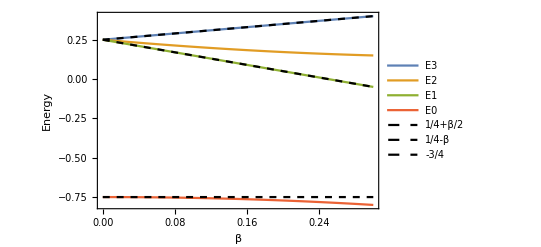

```mathematica
Show[Plot[{1/4 (1+2 b),1/4 (-1-b+√(4+b (-4+9 b))),1/4-b,1/4 (-1-b-√(4+b (-4+9 b)))},{b,0,0.3},Frame->True,FrameLabel->{β, Energy},PlotLegends->{E3,E2,E1,E0}],Plot[b/2+1/4,{b,0,0.3},PlotStyle->{Dashed,Black},PlotLegends->{β/2+1/4}],Plot[-b+1/4,{b,0,0.3},PlotStyle->{Dashed,Black},PlotLegends->{-β+1/4}],
Plot[-3/4,{b,0,0.3},PlotStyle->{Dashed,Black},PlotLegends->{-3/4}]]
```

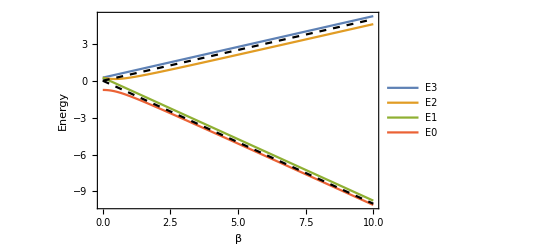

```mathematica
Show[Plot[{1/4 (1+2 b),1/4 (-1-b+√(4+b (-4+9 b))),1/4-b,1/4 (-1-b-√(4+b (-4+9 b)))},{b,0,10},Frame->True,FrameLabel->{β, Energy},PlotLegends->{E3,E2,E1,E0}],Plot[b/2,{b,0,10},PlotStyle->{Dashed,Black}],Plot[-b,{b,0,10},PlotStyle->{Dashed,Black}]]
```

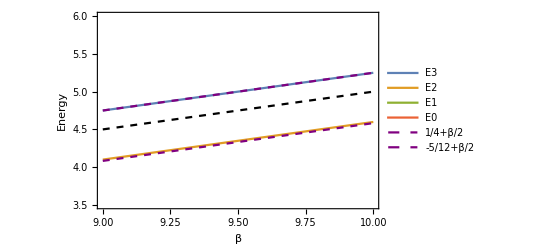

```mathematica
Show[Plot[{1/4 (1+2 b),1/4 (-1-b+√(4+b (-4+9 b))),1/4-b,1/4 (-1-b-√(4+b (-4+9 b)))},{b,9,10},Frame->True,FrameLabel->{β, Energy},PlotLegends->{E3,E2,E1,E0},PlotRange->{3.5,6}],Plot[b/2,{b,9,10},PlotStyle->{Dashed,Black}],Plot[-b,{b,9,10},PlotStyle->{Dashed,Black}],
Plot[b/2+1/4,{b,9,10},PlotStyle->{Dashed,Purple},PlotLegends->{β/2+1/4}],
Plot[b/2-5/12,{b,9,10},PlotStyle->{Dashed,Purple},PlotLegends->{β/2-5/12}]]
```

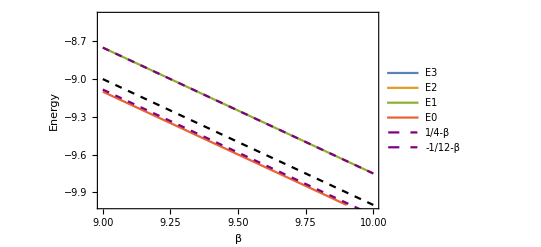

```mathematica
Show[Plot[{1/4 (1+2 b),1/4 (-1-b+√(4+b (-4+9 b))),1/4-b,1/4 (-1-b-√(4+b (-4+9 b)))},{b,9,10},Frame->True,FrameLabel->{β, Energy},PlotLegends->{E3,E2,E1,E0},PlotRange->{-10,-8.5}],Plot[b/2,{b,9,10},PlotStyle->{Dashed,Black}],Plot[-b,{b,9,10},PlotStyle->{Dashed,Black}],
Plot[-b+1/4,{b,9,10},PlotStyle->{Dashed,Purple},PlotLegends->{-β+1/4}],
Plot[-b-1/12,{b,9,10},PlotStyle->{Dashed,Purple},PlotLegends->{-β-1/12}]]
```

```mathematica
3*(1/4 (-1-b-√(4+b (-4+9 b))))+1/4-b+3*1/4 (-1-b+√(4+b (-4+9 b)))+5*1/4 (1+2 b)//FullSimplify
```

0

```mathematica
Tr[HFull]
```

0

```mathematica
(1/2)*Sqrt[1*(1+1)-mL*(mL+1)]*Sqrt[1/2*(1/2+1)-1/2*(1/2-1)]/.{mL->-1}
```

1/(√2)

```mathematica
(1/2)*Sqrt[1*(1+1)-mL*(mL+1)]*Sqrt[1/2*(1/2+1)-1/2*(1/2-1)]/.{mL->0}
```

1/(√2)

```mathematica
(1/2)*Sqrt[1*(1+1)-mL*(mL-1)]*Sqrt[1/2*(1/2+1)-(-1/2)*(-1/2+1)]/.{mL->0}
```

1/(√2)